# Барицентрические координаты. Цвет

КМ, 1 курс, 5 группа
Шклярик В.С.
12-ноя-2021

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
Grid[Take[fioData=Import["VS1P05 ШклярикВера.xlsx",{"Sheets","ФИО"}],2],Frame->All]
Dimensions[fioData=Drop[fioData,2]]
Dimensions/@{PF=fioData⟦All,{2,3}⟧,PI=fioData⟦All,{4,5}⟧,PO=fioData⟦All,{6,7}⟧}
```

C:\Users\asus\Desktop\км\введение в специальность\домашки

ID | Шклярик |  | Вера |  | Сергеевна | 
0. | x | y | x | y | x | y

{17,7}

{{17,2},{17,2},{17,2}}

```mathematica
PF
```

{{7.,95.},{7.,75.},{7.,50.},{7.,25.},{7.,5.},{27.,5.},{50.,25.},{50.,45.},{50.,67.},{50.,45.},{50.,25.},{74.,5.},{93.,5.},{93.,25.},{93.,50.},{93.,75.},{93.,95.}}

```mathematica
initials[P_List,lineColor_:Black]:=Graphics[{{lineColor,Thickness[0.2], Line[P]},{White,PointSize[0.0005], Point/@P,MapIndexed[Tooltip,Point/@P]}},ImageSize->Small]
```

```mathematica
Manipulate[StringForm["`` `` `` ``",Style["ℒ =",Large],Grid[letters//Round,Frame->All],Style["∈ℝ^34 ⟹ ",Large],initials[letters,Switch[letters,PF,Red,PI,Blue,PO,Green]]], {letters, {PF->"Ш", PI->"В", PO->"С"}}]
```

```mathematica
Animate[initials[If[t<1,(1-t) PF+t PI,(2-t) PI+(t-1) PO],Blend[{Red,Blue,Green},t-1/2]],{t,0,2},DefaultDuration->9]
```

## Задание 4.

```mathematica
ClearAll[P1,P2,P3]
```

```mathematica
P={{1,0},{3,4},{7,3},{0,0}};
Color={Green,Blue,Red,Black};
```

```mathematica
Partition[{1, 2, 3, 1}, 2, 1]
```

{{1,2},{2,3},{3,1}}

```mathematica
barCoord=Dynamic[Round[Inverse@Append[P⟦1;;3⟧ᵀ,{1,1,1}].Append[P⟦-1⟧,1],10^-2]//N];
LocatorPane[Dynamic@P,Dynamic@Graphics[{{Red,InfiniteLine@P⟦{1,2}⟧,Blue,InfiniteLine@P⟦{1,3}⟧,Green,InfiniteLine@P⟦{3,2}⟧},{PointSize@Large,MapThread[{#1,Point[#2]}&,{Color,P}]}},PlotLabel->StringForm["`` ⟶ ``",Dynamic[P//Last],MapThread[Style,{barCoord//First,{FontColor->Blue,FontColor->Red,FontColor->Green}}]],Frame->True,PlotRange->{{-10,10},{-10,10}}],Appearance->None]
```

```mathematica
barCoord⟦1,#⟧&{1,2,3}
```

{barCoord⟦1,#1⟧&,2 (barCoord⟦1,#1⟧&),3 (barCoord⟦1,#1⟧&)}

```mathematica
Text[StringForm["``⟶ ``",Dynamic[P//Last],Dynamic[P//Rest]]]
```

⟶

```mathematica
P⟦1;;3⟧
%ᵀ
Append[%,{1,1,1}]
Inverse@%//MatrixForm
%.%%//Chop
```

{{1,0},{3,4},{7,3}}

{{1,3,7},{0,4,3}}

{{1,3,7},{0,4,3},{1,1,1}}

(-1/18 | -2/9 | 19/18
-1/6 | 1/3 | 1/6
2/9 | -1/9 | -2/9)

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Round[Inverse@Append[P⟦1;;3⟧ᵀ,{1,1,1}].Append[P⟦-1⟧,1],10^-2]//N
```

{1.06,0.17,-0.22}

## Задание 5.

```mathematica
ClearAll[Ш,В,С];
Ш=initials[PF,Red];
В=initials[PI,Blue];
С=initials[PO,Green];
```

```mathematica
barCoord=Dynamic[Round[Inverse@Append[P⟦1;;3⟧ᵀ,{1,1,1}].Append[P⟦-1⟧,1],10^-2]//N];
Row[{LocatorPane[Dynamic@P,Dynamic@Graphics[{{Red,InfiniteLine@P⟦{1,2}⟧,Blue,InfiniteLine@P⟦{1,3}⟧,Green,InfiniteLine@P⟦{3,2}⟧},{PointSize@Large,MapThread[{#1,Point[#2]}&,{Color,P}]},Inset[Ш,P⟦3⟧,Center,{1.8,1.8},Background->White],Inset[С,P⟦1⟧,Center,{1.8,1.8},Background->White],Inset[В,P⟦2⟧,Center,{1.8,1.8},Background->White]},PlotLabel->StringForm["`` ⟶ ``",Dynamic[P//Last],MapThread[Style,{barCoord//First,{FontColor->Green,FontColor->Blue,FontColor->Red}}]],Frame->True,PlotRange->{{-10,10},{-10,10}},ImageSize->Medium],Appearance->None],Dynamic@initials[(List@@barCoord)⟦1,1⟧*PO+(List@@barCoord)⟦1,2⟧*PI+(List@@barCoord)⟦1,3⟧*PF,Blend[{Green,Blue,Red},barCoord//Last]]},StringForm["``",Style["    ⟹    " ,Large]]]
```

⟹

```mathematica
barCoord=Dynamic[Round[Inverse@Append[P⟦1;;3⟧ᵀ,{1,1,1}].Append[P⟦-1⟧,1],10^-2]//N]
```

```mathematica
(List@@barCoord)⟦1,1⟧
```

1.06

```mathematica
ClearAll[S];
S=Dynamic[(List@@barCoord)⟦1,1⟧*PI+(List@@barCoord)⟦1,2⟧*PF+(List@@barCoord)⟦1,3⟧*PO]
```

```mathematica
DynamicModule
```

DynamicModule

```mathematica
initials[S];
```

```mathematica
MapThread[List,{{Ш, В, С},P⟦#⟧&/@{1,2,3}}];
```

```mathematica
Inset@MapThread[List,{{Ш, В, С},P⟦#⟧&/@{1,2,3}}];
```

## Задание 6.

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
Grid[Append[Take[ColorsData=Import["VS1P05 ШклярикВера.xlsx",{"Sheets","Цвета"}],2],Range@Length@First@ColorsData],Frame->All]
Dimensions[ColorsData=Drop[ColorsData,2]]
Colors=RGBColor[#5,#6,#7]&@@@ColorsData
```

C:\Users\asus\Desktop\км\введение в специальность\домашки

id | Метка
цвета | Русское
название | Английское
название | Цветовые компоненты |  |  |  |  |  |  |  Модель RGB |  |  | Модель HSL |  |  | Модель HSB |  | 
 |  |  |  | Red | Green | Blue | Hue | Saturation | Lightness | Brightness | x | y | z | x | y | z | x | y | z
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

{24,20}

{RGBColor[1., 0., 0.],RGBColor[1., 1., 0.],RGBColor[0., 1., 0.],RGBColor[0., 1., 1.],RGBColor[0., 0., 1.],RGBColor[1., 0., 1.],RGBColor[0.5, 0., 0.],RGBColor[1., 0.5, 0.5],RGBColor[1., 1., 0.5],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 1., 1.],RGBColor[0.5, 0.5, 1.],RGBColor[1., 0.5, 1.],RGBColor[0.5, 0.5, 0.],RGBColor[0., 0.5, 0.],RGBColor[0., 0.5, 0.5],RGBColor[0., 0., 0.5],RGBColor[0.5, 0., 0.5],RGBColor[0., 0., 0.],RGBColor[0.25, 0.25, 0.25],RGBColor[0.5, 0.5, 0.5],RGBColor[0.75, 0.75, 0.75],RGBColor[1., 1., 1.],RGBColor[,,]}

```mathematica
Dimensions[spaceRGB=ColorsData⟦All,12;;14⟧];
Dimensions[spaceRGB1=RotationTransform[{{1,1,1},{0,0,1}}]/@spaceRGB];
Dimensions[spaceHSL=ColorsData⟦All,15;;17⟧];
Dimensions[spaceHSB=ColorsData⟦All,18;;20⟧];
```

```mathematica
ColorsData
```

{{0.,R,Красный,Red,1.,0.,0.,0.,1.,0.5,1.,1.,0.,0.,1.,0.,0.5,1.,0.,1.},{1.,Y,Жёлтый,Yellow,1.,1.,0.,60.,1.,0.5,1.,1.,1.,0.,0.5,0.866025,0.5,0.5,0.866025,1.},{2.,G,Зелёный,Green,0.,1.,0.,120.,1.,0.5,1.,0.,1.,0.,-0.5,0.866025,0.5,-0.5,0.866025,1.},{3.,C,Синюшный,Cyan,0.,1.,1.,180.,1.,0.5,1.,0.,1.,1.,-1.,1.22515×10^-16,0.5,-1.,1.22515×10^-16,1.},{4.,B,Синий,Blue,0.,0.,1.,240.,1.,0.5,1.,0.,0.,1.,-0.5,-0.866025,0.5,-0.5,-0.866025,1.},{5.,M,Пурпурный,Magenta,1.,0.,1.,300.,1.,0.5,1.,1.,0.,1.,0.5,-0.866025,0.5,0.5,-0.866025,1.},{6.,DR,Тёмно-красный,Dark Red,0.5,0.,0.,0.,0.5,0.25,0.5,0.5,0.,0.,0.5,0.,0.25,0.5,0.,0.5},{7.,LR,Светло-красный,Light Red,1.,0.5,0.5,0.,0.5,0.75,1.,1.,0.5,0.5,0.5,0.,0.75,0.5,0.,1.},{8.,LY,Светло-жёлтый,Light Yellow,1.,1.,0.5,60.,0.5,0.75,1.,1.,1.,0.5,0.25,0.433013,0.75,0.25,0.433013,1.},{9.,LG,Светло-зелёный,Light Green,0.5,1.,0.5,120.,0.5,0.75,1.,0.5,1.,0.5,-0.25,0.433013,0.75,-0.25,0.433013,1.},{10.,LC,Светло-синюшный,Light Cyan,0.5,1.,1.,180.,0.5,0.75,1.,0.5,1.,1.,-0.5,6.12574×10^-17,0.75,-0.5,6.12574×10^-17,1.},{11.,LB,Светло-синий,Light Blue,0.5,0.5,1.,240.,0.5,0.75,1.,0.5,0.5,1.,-0.25,-0.433013,0.75,-0.25,-0.433013,1.},{12.,LM,Светло-пурпурный,Light Magenta,1.,0.5,1.,300.,0.5,0.75,1.,1.,0.5,1.,0.25,-0.433013,0.75,0.25,-0.433013,1.},{13.,DY,Тёмно-жёлтый,Dark Yellow,0.5,0.5,0.,60.,0.5,0.25,0.5,0.5,0.5,0.,0.25,0.433013,0.25,0.25,0.433013,0.5},{14.,DG,Тёмно-зелёный,Dark Green,0.,0.5,0.,120.,0.5,0.25,0.5,0.,0.5,0.,-0.25,0.433013,0.25,-0.25,0.433013,0.5},{15.,DC,Тёмно-синюшный,Dark Cyan,0.,0.5,0.5,180.,0.5,0.25,0.5,0.,0.5,0.5,-0.5,6.12574×10^-17,0.25,-0.5,6.12574×10^-17,0.5},{16.,DB,Тёмно-синий,Dark Blue,0.,0.,0.5,240.,0.5,0.25,0.5,0.,0.,0.5,-0.25,-0.433013,0.25,-0.25,-0.433013,0.5},{17.,DM,Тёмно-пурпурный,Dark Magenta,0.5,0.,0.5,300.,0.5,0.25,0.5,0.5,0.,0.5,0.25,-0.433013,0.25,0.25,-0.433013,0.5},{18.,K,Чёрный,Black,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{19.,Dgy,Тёмно-серый,Dark Gray,0.25,0.25,0.25,0.,0.,0.25,0.25,0.25,0.25,0.25,0.,0.,0.25,0.,0.,0.25},{20.,Gy,Серый,Gray,0.5,0.5,0.5,0.,0.,0.5,0.5,0.5,0.5,0.5,0.,0.,0.5,0.,0.,0.5},{21.,Lgy,Светло-серый,Light Gray,0.75,0.75,0.75,0.,0.,0.75,0.75,0.75,0.75,0.75,0.,0.,0.75,0.,0.,0.75},{22.,W,Белый,White,1.,1.,1.,0.,0.,1.,1.,1.,1.,1.,0.,0.,1.,0.,0.,1.},{,,,,,,,,,,,,,,,,,,,}}

```mathematica
spaceRGB=ColorsData⟦All,12;;14⟧
```

{{1.,0.,0.},{1.,1.,0.},{0.,1.,0.},{0.,1.,1.},{0.,0.,1.},{1.,0.,1.},{0.5,0.,0.},{1.,0.5,0.5},{1.,1.,0.5},{0.5,1.,0.5},{0.5,1.,1.},{0.5,0.5,1.},{1.,0.5,1.},{0.5,0.5,0.},{0.,0.5,0.},{0.,0.5,0.5},{0.,0.,0.5},{0.5,0.,0.5},{0.,0.,0.},{0.25,0.25,0.25},{0.5,0.5,0.5},{0.75,0.75,0.75},{1.,1.,1.},{,,}}

## Задание 7.

```mathematica
Table[{RGBColor@(spaceRGB⟦i⟧),Sphere[spaceRGB⟦i⟧,0.1]},{i,1,23}]
```

{{RGBColor[{1., 0., 0.}],Sphere[{1.,0.,0.},0.1]},{RGBColor[{1., 1., 0.}],Sphere[{1.,1.,0.},0.1]},{RGBColor[{0., 1., 0.}],Sphere[{0.,1.,0.},0.1]},{RGBColor[{0., 1., 1.}],Sphere[{0.,1.,1.},0.1]},{RGBColor[{0., 0., 1.}],Sphere[{0.,0.,1.},0.1]},{RGBColor[{1., 0., 1.}],Sphere[{1.,0.,1.},0.1]},{RGBColor[{0.5, 0., 0.}],Sphere[{0.5,0.,0.},0.1]},{RGBColor[{1., 0.5, 0.5}],Sphere[{1.,0.5,0.5},0.1]},{RGBColor[{1., 1., 0.5}],Sphere[{1.,1.,0.5},0.1]},{RGBColor[{0.5, 1., 0.5}],Sphere[{0.5,1.,0.5},0.1]},{RGBColor[{0.5, 1., 1.}],Sphere[{0.5,1.,1.},0.1]},{RGBColor[{0.5, 0.5, 1.}],Sphere[{0.5,0.5,1.},0.1]},{RGBColor[{1., 0.5, 1.}],Sphere[{1.,0.5,1.},0.1]},{RGBColor[{0.5, 0.5, 0.}],Sphere[{0.5,0.5,0.},0.1]},{RGBColor[{0., 0.5, 0.}],Sphere[{0.,0.5,0.},0.1]},{RGBColor[{0., 0.5, 0.5}],Sphere[{0.,0.5,0.5},0.1]},{RGBColor[{0., 0., 0.5}],Sphere[{0.,0.,0.5},0.1]},{RGBColor[{0.5, 0., 0.5}],Sphere[{0.5,0.,0.5},0.1]},{RGBColor[{0., 0., 0.}],Sphere[{0.,0.,0.},0.1]},{RGBColor[{0.25, 0.25, 0.25}],Sphere[{0.25,0.25,0.25},0.1]},{RGBColor[{0.5, 0.5, 0.5}],Sphere[{0.5,0.5,0.5},0.1]},{RGBColor[{0.75, 0.75, 0.75}],Sphere[{0.75,0.75,0.75},0.1]},{RGBColor[{1., 1., 1.}],Sphere[{1.,1.,1.},0.1]}}

```mathematica
Graphics3D[Table[{RGBColor@(spaceRGB⟦i⟧),Sphere[spaceRGB⟦i⟧,0.15]},{i,1,23}],Axes->True,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
spaceRGB
```

{{1.,0.,0.},{1.,1.,0.},{0.,1.,0.},{0.,1.,1.},{0.,0.,1.},{1.,0.,1.},{0.5,0.,0.},{1.,0.5,0.5},{1.,1.,0.5},{0.5,1.,0.5},{0.5,1.,1.},{0.5,0.5,1.},{1.,0.5,1.},{0.5,0.5,0.},{0.,0.5,0.},{0.,0.5,0.5},{0.,0.,0.5},{0.5,0.,0.5},{0.,0.,0.},{0.25,0.25,0.25},{0.5,0.5,0.5},{0.75,0.75,0.75},{1.,1.,1.},{,,}}

```mathematica
Graphics3D[Table[{Colors⟦i⟧,Tooltip[Sphere[spaceHSL⟦i⟧,0.15],ColorsData⟦i,3⟧]},{i,1,23}],Axes->True,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Graphics3D[Table[{Colors⟦i⟧,Sphere[spaceRGB⟦i⟧,0.15]},{i,1,23}],Axes->True,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
spaceHSB
spaceHSL
```

{{1.,0.,1.},{0.5,0.866025,1.},{-0.5,0.866025,1.},{-1.,1.22515×10^-16,1.},{-0.5,-0.866025,1.},{0.5,-0.866025,1.},{0.5,0.,0.5},{0.5,0.,1.},{0.25,0.433013,1.},{-0.25,0.433013,1.},{-0.5,6.12574×10^-17,1.},{-0.25,-0.433013,1.},{0.25,-0.433013,1.},{0.25,0.433013,0.5},{-0.25,0.433013,0.5},{-0.5,6.12574×10^-17,0.5},{-0.25,-0.433013,0.5},{0.25,-0.433013,0.5},{0.,0.,0.},{0.,0.,0.25},{0.,0.,0.5},{0.,0.,0.75},{0.,0.,1.},{,,}}

{{1.,0.,0.5},{0.5,0.866025,0.5},{-0.5,0.866025,0.5},{-1.,1.22515×10^-16,0.5},{-0.5,-0.866025,0.5},{0.5,-0.866025,0.5},{0.5,0.,0.25},{0.5,0.,0.75},{0.25,0.433013,0.75},{-0.25,0.433013,0.75},{-0.5,6.12574×10^-17,0.75},{-0.25,-0.433013,0.75},{0.25,-0.433013,0.75},{0.25,0.433013,0.25},{-0.25,0.433013,0.25},{-0.5,6.12574×10^-17,0.25},{-0.25,-0.433013,0.25},{0.25,-0.433013,0.25},{0.,0.,0.},{0.,0.,0.25},{0.,0.,0.5},{0.,0.,0.75},{0.,0.,1.},{,,}}

```mathematica
Graphics3D[Table[{Colors⟦i⟧,Sphere[spaceHSB⟦i⟧,0.15]},{i,1,23}],Axes->True,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Graphics3D[Table[{Colors⟦i⟧,Sphere[spaceRGB1⟦i⟧,0.15]},{i,1,23}],Axes->True,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Table[{Colors⟦i⟧,Tooltip[Sphere[Part[colorSpace,i],0.1],Text[Style[ColorsData⟦i,3⟧,Colors⟦i⟧,Bold,Medium],
Background->If[i≠23&&i≠9&&i≠2,White,Gray]]]},{i,1,23}],Axes->False,Lighting->"Neutral",ImageSize->Large,Boxed->False],{colorSpace,{spaceRGB->"RGB",spaceRGB1->"rotRGB ",spaceHSL->"HSL",spaceHSB->"HSB"}}]
```

```mathematica
RGBColor/@spaceRGB⟦{-6,-5,-4,-3}⟧
Line[{Part[spaceRGB,Range[0,6]]}]
```

{RGBColor[{0., 0., 0.}],RGBColor[{0.25, 0.25, 0.25}],RGBColor[{0.5, 0.5, 0.5}],RGBColor[{0.75, 0.75, 0.75}]}

Line[{{List,{1.,0.,0.},{1.,1.,0.},{0.,1.,0.},{0.,1.,1.},{0.,0.,1.},{1.,0.,1.}}}]

```mathematica
Manipulate[Graphics3D[Table[{Colors⟦i⟧,Tooltip[Sphere[Part[colorSpace,i],0.1],Text[Style[ColorsData⟦i,3⟧,Colors⟦i⟧,Bold,Medium],
Background->If[i≠23&&i≠9&&i≠2,White,Gray]]],Black,Dashed,Thick,Line[{Part[colorSpace,{-6,-5,-4,-3,-2}]}],RGBColor@spaceRGB⟦-5⟧,Line[{Part[colorSpace,{1,2,3,4,5,6,1}]}],RGBColor@spaceRGB⟦-4⟧,Line[{Part[colorSpace,{7,14,15,16,17,18,7}]}],RGBColor@spaceRGB⟦-3⟧,Line[{Part[colorSpace,{8,9,10,11,12,13,8}]}]},{i,1,23}],Axes->False,Lighting->"Neutral",ImageSize->Large,Boxed->False],{colorSpace,{spaceRGB->"RGB",spaceRGB1->"rotRGB ",spaceHSL->"HSL",spaceHSB->"HSB"}}]
```

## Задание 8.

```mathematica
ClearAll[Surf];
T={{1,9,3},{-1,3,6},{12,-4,5},{10,4,-6}};
Surf[s_,t_]:={(1-t) (1-s),(1-t)s  ,t (1-s) ,t s }.T
```

```mathematica
Surf[s,t];
Dimensions@%
```

{3}

```mathematica
P0=(1-s) B0[t]+s B1[t]+(1-t) R0[s]+t R1[s]/.{{t->0,s->0},{t->0,s->1/2},{t->1/2,s->0},{t->1/2,s->1/2}}
```

{{0,0,0.},{0,1,0.},{1,0,0.},{1,1,0.}}

```mathematica
Show[Graphics3D[{Black,PointSize@0.015,Point@T}],ParametricPlot3D[Surf[s,t],{s,0,1},{t,0,1},MeshStyle->{Red, Blue},Lighting->"Neutral"],Boxed->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{t,0,Sin[t]},{t,2π,-Sin[t]},{0,t,Sin[t]},{2π,t,-Sin[t]}},{t,0,2 π},PlotStyle->{Blue,Blue,Red,Red}]
```

-Graphics3D-

```mathematica
n=0.2;
B0[t_]:={t,0,n Sin[2 π t]};
B1[t_]:={t,1,-n Sin[2 π t]};R0[t_]:={0,t,n Sin[2 π t]};R1[t_]:={1,t,-n Sin[2 π t]};
```

```mathematica
Fig1=Show[Graphics3D[{Black,PointSize@0.02,Point@P0}],FigB=ParametricPlot3D[{B0[t],B1[t]},{t,0,1},PlotStyle->Blue],
FigR=ParametricPlot3D[{R0[t],R1[t]},{t,0,1},PlotStyle->Red],ImageSize->Automatic]
```

-Graphics3D-

## Задание 9.

```mathematica
{Show[Fig1,ParametricPlot3D[{(1-s) B0[t]+s B1[t]},{t,0,1},{s,0,1}
,MeshStyle->{Blue,None},Lighting->"Neutral"],ImageSize->300,Boxed->False],Show[Fig1,ParametricPlot3D[{(1-t) R0[s]+t R1[s]},{t,0,1},{s,0,1},MeshStyle->{Red,None},Lighting->"Neutral"],ImageSize->300,Boxed->False]}
```

{-Graphics3D-,-Graphics3D-}

## Задание 10.

```mathematica
P0=(1-s) B0[t]+s B1[t]+(1-t) R0[s]+t R1[s]/.{{t->0,s->0},{t->0,s->1/2},{t->1/2,s->0},{t->1/2,s->1/2}}
```

{{0,0,0.},{0,1,0.},{1,0,0.},{1,1,0.}}

```mathematica
Show[Fig1,ParametricPlot3D[(1-s) B0[t]+s B1[t]+(1-t) R0[s]+t R1[s]-({(1-t) (1-s),(1-t)s ,t (1-s) ,t s }.P0),{t,0,1},{s,0,1},Lighting->"Neutral",MeshStyle->{Red, Blue}],PlotRange->All,Boxed->False,ImageSize->500]
```

-Graphics3D-

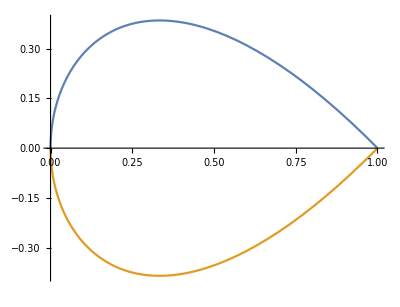

```mathematica
Show[ParametricPlot[{{t^2,t-t^3},{t^2,-t+t^3}},{t,0,1}]]
```

```mathematica
Fig2=Show[ParametricPlot3D[{{0,t^2,t-t^3},{0,-t^2,-t+t^3},{t^2,0,t-t^3},{-t^2,0,t-t^3}},{t,-1,1},PlotRange->All,Axes->False]]
```

-Graphics3D-

```mathematica
L0[t_]:={0,t^2,t-t^3};L1[t_]:={0,-t^2,-t+t^3};L2[t_]:={t^2,0,t-t^3};L3[t_]:={-t^2,0,t-t^3};
```

```mathematica
Show[Fig2,ParametricPlot3D[(1-s) L0[t]+s L1[t]+(1-t) L2[s]+t L3[s],{t,0,1},{s,0,1},Lighting->"Neutral",MeshStyle->{Red, Blue}],PlotRange->All,Boxed->False,ImageSize->500]
```

-Graphics3D-

```mathematica
{Show[Fig2,ParametricPlot3D[{(1-t) L1[s]+t L2[s]},{t,0,1},{s,-1,1},MeshStyle->{Blue,None},Lighting->"Neutral"],ImageSize->300,Boxed->False],
Show[Fig2,ParametricPlot3D[{(1-t) L1[s]+t L3[s]},{t,0,1},{s,-1,1},MeshStyle->{Red,None},Lighting->"Neutral"],ImageSize->300,Boxed->False],
Show[Fig2,ParametricPlot3D[{t  L0[s]+(t-1) L2[s]},{t,0,1},{s,-1,1},MeshStyle->{Blue,None},Lighting->"Neutral"],ImageSize->300,Boxed->False],
Show[Fig2,ParametricPlot3D[{(t-1)  L3[s]+t L0[s]},{t,0,1},{s,-1,1},MeshStyle->{Blue,None},Lighting->"Neutral"],ImageSize->300,Boxed->False]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[Fig2,ParametricPlot3D[{(1-t) L1[s]+t L2[s]},{t,0,1},{s,-1,1},MeshStyle->{Gray,None},Lighting->{{"Directional",Pink,{{0,0,1},{0,1,0}}}}],
ParametricPlot3D[{(1-t) L1[s]+t L3[s]},{t,0,1},{s,-1,1},MeshStyle->{Pink,None},Lighting->{{"Directional",Pink,{{0,0,1},{0,2,0}}}}],
ParametricPlot3D[{t  L0[s]+(t-1) L2[s]},{t,0,1},{s,-1,1},MeshStyle->{Gray,None},Lighting->{{"Directional",Pink,{{0,0,1},{0,1,0}}}}],
ParametricPlot3D[{(t-1)  L3[s]+t L0[s]},{t,0,1},{s,-1,1},MeshStyle->{Pink,None},Lighting->{{"Directional",Pink,{{0,0,1},{0,1,0}}}}],ImageSize->500,Boxed->False]
```

-Graphics3D-